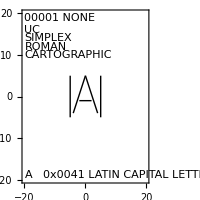

```mathematica
rev[l_] := Map[# *{1,-1}&,l];

ends[l_] := With[{},
Replace[l,{a:{{x1_,y1_,n_},{_,_,_}},b___,c:{{_,_,_},{x2_,y2_,n2_}}} -> {{{x1,y1,2},{x1,y1,0}},a,b,c,{{x2,y2,0},{x2,y2,2}}}]
];

d3[l_] := With[{},
ReplaceRepeated[l,{xx__,PatternSequence[{{x1_,y1_},{-50,0}} ,{{-50,0},{x2_,y2_}}],yy__} -> {xx,{{x1,y1,0},{x1,y1,1}},{{x1,y1,1},{x2,y2,1}},{{x2,y2,1},{x2,y2,0}},yy}] //. {x_?NumberQ,y_?NumberQ}:> {x,y,0}
];

decode[s_] := With[{ss = ToCharacterCode[s]-ToCharacterCode@StringReplace[s,_->"R"]},
Map[Line,ends@d3@Partition[rev@Partition[ss,2],2,1]]
];

parse[line_String] := With[{
lno = FromDigits[StringTrim@StringTake[line,5]],
ccnt = FromDigits[StringTrim@StringTake[line,{6,8}]],
slen = StringLength@StringDrop[line,8],
lr = ToCharacterCode[StringTake[line,{9,10}]]-ToCharacterCode["RR"],
rem = StringDrop[line,10]},
If[2 ccnt ≠ slen,Throw[{"hershey line error",lno,ccnt,slen}]];
With[{dec = decode[rem]},
<|"hid"->lno,"lr"->lr,"gr3d"->gr3d@@dec,"line"->line|>
]];

hersheyfonts[fname_String] := With[{listoflines = Select[Import[fname,"List"],Not[StringStartsQ[#,"#"]]&]},
Map[parse,listoflines]
];

 hersheydb = Dataset@hersheyfonts[NotebookDirectory[] <> "hersheyfonts.txt"];




z02d[gr3d[l___]] := gr2d@@Cases[{l},Line[{{x1_,y1_,0},{x2_,y2_,0}}]:>Line[{{x1,y1},{x2,y2}}]];
hersheydb = hersheydb[All,<| #,"gr2d"->z02d[#gr3d]|>&];



charname=Composition[
With[{arg=#},If[MissingQ[arg],"NONE",arg]]&,Association[With[{rules=Map[StringSplit[StringTrim[#]," ",2]/.{a_,b_}:>Rule[Interpreter["Integer"][a],b]&,Select[Import[NotebookDirectory[] <> "hersheyindex.txt","Lines"],Not[StringStartsQ[#,"#"]]&]]},rules]]];
hersheydb = hersheydb[All,<|#,"hname"->charname[#hid]|>&];



f[fn_Integer,hn_Integer,str_] :=Sequence@MapIndexed[{fn+hn-1+First@#2,hn,#1}&,StringPartition[str,1]];
f[fn_Integer,hn_Integer,s1_,s2_] :=Sequence@MapIndexed[{fn+hn-1+First@#2,hn,#1}&,CharacterRange[s1,s2]];
SetAttributes[f,Listable];
fontmap = Flatten[#,2]&@{
f[1,{0,500,1000,2000,2500,3000,3300,3500,3800},"A","Z"]
,f[1,{550,1050,2000,2500,3000},"A","Z"]
,f[51,{550,1050,2000,2500,3000},"A","Z"]
,f[101,{500,1000,2000,2500,3000,3300,3500,3800},"a","z"]
,f[151,{1000,2000,3000},"a","z"]
,f[151,{500,2500},"a","z"]
,f[177,{1000,2000},"ﬀﬁﬂﬃﬄ"]
,f[191,{ 1000,2000},"ﬀﬁﬂﬃﬄ"]
,f[200,{2500,3000,3500},"0123456789.,:;!?‘’&$/()*-+=′″°"]
,f[250,{2500,3000             },"0123456789.,:;!?‘’&$/()*-+=′″°"]

,f[27,{0,500,1000,2000},"Α","Ρ"]
,f[44,{0,500,1000,2000},"Σ","Ω"]
,f[83,{500},"∇"]
,f[127,{500,1000,2000},"α","ρ"]
,f[144,{500,1000,2000},"σ","ω"]
,f[200,{0,500},"0123456789.,:;!?′″°$/()|-+=×*·‘’→#&⌑Y∥⊥∠⸫♤♡♢♧☘⚜"]
,f[200,{1000,2000},"0123456789.,:;!?′″°*/()[]{}⟨⟩|∥−+±∓⨯⋅÷=≠≡<>≦≧∝∼̛̂̀́̆̓̒̔√⊂∪⊃∩∈→↑←↓Y∇√∫∮∞%&@$#§†‡∃"]
,f[77,{2000},"ℵ"]
,f[1,{2800},"А","Я"]
,f[101,{2800},"а","я"]
,f[1,{1400,2400},"ΠΣ()[]{}⎰⎱√∫"]
,f[-3,{200,700,1200,2200,2700,2750,3200,3250,3700},"​  "]
,f[184,{500,1000,2000},"εθϕϚ"]
,f[323,{2000,2050},"♯♮♭"]
,f[0,{2190},"℘"]
};
fm1 = Association@@(fontmap /. {hid_,fid_,chr_} :> (hid->chr));
fm2[n_Integer] := With[{v=fm1[n]},If[MissingQ[v],"�",v]];
 pat=With[{lines=Select[Import[NotebookDirectory[] <> "hersheyclasses.txt","Lines"],Not[StringStartsQ[#,"#"]]&]},
With[{lines1 = Map[StringSplit[StringReplace[StringTrim[#]," "..->" "]," "] /. {a_,b__} :> {Interpreter["Integer"][a],b}&,lines]},
With[{pat=Replace[lines1,{a_,b__} :> {Alternatives@@Range[a,a+If[MemberQ[{b},"NUMERALS"],10,26]-1],Alternatives[b],{b}},1]},
pat]
]];
isa[hid_,a_,nota_]:= Intersection[a,SelectFirst[pat,MatchQ[hid,#[[1]]]&,{1,2,{3}}][[3]]] /. {}:>{nota};
hersheydb = hersheydb[All,<|#,
"unicode"->First@ToCharacterCode@fm2[#hid],
"case"->First@isa[#hid,{"LC","UC"},"NA"],
"strokes"->First@isa[#hid,{"SIMPLEX","DUPLEX","COMPLEX","GOTHIC"},"NA"],
"alphabet"->First@isa[#hid,{"ROMAN","GREEK","CYRILLIC","GERMAN","ITALIAN","ENGLISH"},"NA"],
"size"->First@isa[#hid,{"CARTOGRAPHIC","INDEX","PRIN"},"NA"]
|>&];

doit[n_] := With[{x1=-20,x2=20,y1=-20,y2=20,sc=4,fs=8,xy=200},Graphics[#,Frame->True,ImageSize->{xy,xy},AspectRatio->1,PlotRange->{{x1,x2},{y1,y2}},BaseStyle->{FontSize->fs,FontWeight->Plain}]&@Normal@hersheydb[Select[#hid == n&],{
Composition[Apply[List]][#gr2d],
Text[FromCharacterCode[#unicode],{x1,y1},{-1,-1},BaseStyle->{FontSize->60}],
Inset[TextCell["0x"<>IntegerString[#unicode,16,4] <> " " <>CharacterName[#unicode,"UnicodeName"],PageWidth-> sc(x2-x1)],{0.7 x1, y1},{-1,-1}],
Inset[TextCell[IntegerString[#hid,10,5] <> " " <>#hname,PageWidth->sc(x2-x1)],{x1,y2},{-1,1}],
{Line[{{#lr[[1]],-5},{#lr[[1]],+5}}],Line[{{#lr[[2]],-5},{#lr[[2]],+5}}]},
Text[#case,{x1,0.8 y2},{-1,0}],
Text[#strokes,{x1,0.7 y2},{-1,0}],
Text[#alphabet,{x1,0.6 y2},{-1,0}],
Text[#size,{x1,0.5 y2},{-1,0}]
}&
]];
doit[1]
```

```mathematica
Export["~/Desktop/t.pdf",GraphicsGrid[Partition[Table[doit[i],{i,Normal@hersheydb[Select[0 ≤ #hid < 500 &],"hid"]}],4]],"PDF"]
```